```mathematica
a0 = 0.5 10^-10;
abg = -750 a0;
n = 10^17;
T = 10^-6;
m = 7 10^-26;
kB = 10^-23;
hbar = 10^-34;
v = √((kB T)/m);
k = √(2m kB T/hbar^2);
tof = 4 10^-3;
a[B_,B1_,DB1_,B2_,DB2_,B3_,DB3_]:=abg*(1+DB1/(B-B1))(1+DB2/(B-B2))(1+DB3/(B-B3));
a[B_,B1_,BZ1_,B2_,BZ2_,B3_,BZ3_]:=abg*((B-BZ1)/(B-B1))((B-BZ2)/(B-B2))((B-BZ3)/(B-B3));
a[B_,B1_,BZ1_,B2_,BZ2_,B3_,BZ3_]:=abg((B-BZ1)(B-B2)(B-B3)+(B-BZ2)(B-B1)(B-B3)+(B-BZ3)(B-B1)(B-B2)-k^2 abg^2(B-BZ1)(B-BZ2)(B-BZ3))/((B-B1)(B-B2)(B-B3)-k^2 abg^2(B-BZ1)(B-BZ2)(B-B3)-k^2 abg^2(B-BZ2)(B-BZ3)(B-B1)-k^2 abg^2(B-BZ1)(B-BZ3)(B-B2))
```

```mathematica
k abg
```

-0.443706

```mathematica
n abg^2 v tof
```

0.00336158

```mathematica
Manipulate
```

```mathematica
B1=81.6;DB1=.34; (*DB1=0.34*)
B2=90.47;DB2=7.9;
B3=111.8;DB3=19;
Manipulate[Show[GraphicsColumn[{
 Plot[a[B,B1,DB1,B2,DB2,B3,DB3]/a0,{B,30,140},AspectRatio->0.3,PlotRange->{-5000,5000}],
 Plot[-1/(a[B,B1,DB1,B2,DB2,B3,DB3]/a0)^2 Sign[a[B,B1,DB1,B2,DB2,B3,DB3]],{B,30,140},AspectRatio->0.3,PlotRange->{-0.00001,0.00001},PlotPoints->1000],
Show[Plot[1+1 Exp[-10 n v tof 4π a[B,B1,DB1,B2,DB2,B3,DB3]^2/(1+k^2 a[B,B1,DB1,B2,DB2,B3,DB3]^2)],{B,30,140},AspectRatio->0.3,PlotRange->{1,2}],
Plot[1+.5Exp[-200 n v tof 4π a[B,B1,DB1,B2,DB2,B3,DB3]^2/(1+k^2 a[B,B1,DB1,B2,DB2,B3,DB3]^2)],{B,30,140},AspectRatio->0.3,PlotStyle->Darker[Green],PlotRange->{1,2}]]},Left]],{{B1,81.6},50,150},{{B2,90.47},50,150},{{B3,111.8},50,150},{{DB1,B1-1},50,150},{{DB2,B2-8},50,150},{{DB3,B3-19},50,150}]
```

1.15095×10^6

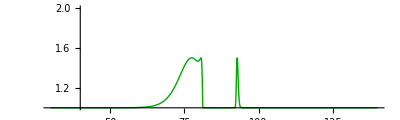

```mathematica
B1=81.6;DB1=1; (*DB1=0.34*)
B2=90.47;DB2=13;
B3=111.8;DB3=19;
a[B,B1,DB1,B2,DB2,B3,DB3]^2/(1+k^2 a[B,B1,DB1,B2,DB2,B3,DB3]^2)/a0^2/.B->150
Plot[1+.5Exp[-500 n v tof 4π a[B,B1,DB1,B2,DB2,B3,DB3]^2/(1+k^2 a[B,B1,DB1,B2,DB2,B3,DB3]^2)],{B,30,140},AspectRatio->0.3,PlotStyle->Darker[Green],PlotRange->{1,2}]
```

```mathematica
k a = - Tan[x+y+z] = (Tan[x+y]+Tan[z])/(1-Tan[x+y]Tan[z])=(Tan[x]+Tan[y]+Tan[z](1-Tan[x]Tan[y]))/(1-Tan[x]Tan[y]-(Tan[x]+Tan[y])Tan[z])=(Tan[x]+Tan[y]+Tan[z]-Tan[x]Tan[y]Tan[z])/(1-Tan[x]Tan[y]-Tan[x]Tan[z]-Tan[y]Tan[z])
```

```mathematica
(k a1+k a2+k a3-k^3 a1 a2 a3)/(1-k^2 a1 a2-k^2 a2 a3-k^2 a1 a3)
```

```mathematica
(k(B-BZ1)/(B-B1)+k(B-BZ2)/(B-B2)+k(B-BZ3)/(B-B3)-k^3(B-BZ1)/(B-B1)(B-BZ2)/(B-B2)(B-BZ3)/(B-B3))/(1-k^2(B-BZ1)/(B-B1)(B-BZ2)/(B-B2)-k^2(B-BZ2)/(B-B2)(B-BZ3)/(B-B3)-k^2(B-BZ1)/(B-B1)(B-BZ3)/(B-B3))
```

```mathematica
(k(B-BZ1)(B-B2)(B-B3)+k(B-BZ2)(B-B1)(B-B3)+k(B-BZ3)(B-B1)(B-B2)-k^3(B-BZ1)(B-BZ2)(B-BZ3))/((B-B1)(B-B2)(B-B3)-k^2(B-BZ1)(B-BZ2)(B-B3)-k^2(B-BZ2)(B-BZ3)(B-B1)-k^2(B-BZ1)(B-BZ3)(B-B2))
```